```mathematica
Get[FileNameJoin[{NotebookDirectory[],"bouyancy.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"visualizations.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"COM.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"Stability.m"}]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"boats.m"}]]
```

```mathematica
avs[boat_,front_,guess_]:=Module[{},
FindRoot[rightingArm[boat,front,θ],{θ,guess},AccuracyGoal->2,PrecisionGoal->Infinity (*only accuracy used*)]
]
```

```mathematica
ClearAll[rightingArm]
```

```mathematica
rightingArm[boat,{0,1,0},θ]
```

rightingArm[<|name→A cube,massPts→{{0,0,0}},masses→{100},region→-Graphics3D-,graphics:>Show[-Graphics3D-,-Graphics3D-]|>,{0,1,0},θ]

```mathematica
nPoints=1000
```

1000

```mathematica
boatWaterline[boat,{0,0,1}]
```

111.769

1.04637

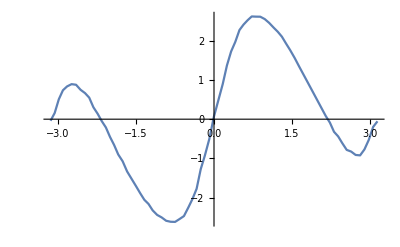

```mathematica
Plot[rightingArm[boat,{0,1,0},θ],{θ,-Pi,Pi},PlotPoints->20,MaxRecursion->2]
```

```mathematica
HoldForm@rightingArm[boat,{0,1,0},θ]
```

rightingArm[boat,{0,1,0},θ]

```mathematica
avs[boat,{1,0,0},-Pi/3]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{θ→-1.0472}